## Calculate the Legendre Polynomials for a given quantum number n

```mathematica
polys[n_]:=Table[LegendreP[n,m,Cos[θ]],{m,-n,n,1}];
```

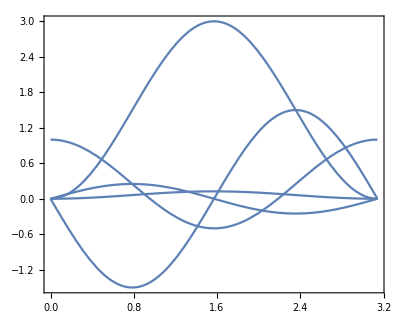

```mathematica
Plot[polys[2],{θ,0,π},PlotStyle->Automatic,Frame->True,Axes->False,AspectRatio->0.8]
```